# JAGROS, d.o.o.

```mathematica
Labeled[Import["C:\Users\HP\Desktop\Računalniška orodja v matematiki\Logotip podjetja.png"],
	       Text["Slika 1: Logotip podjetja"]]
```

-Graphics-Slika 1: Logotip podjetja

## OSNOVNI PODATKI

- JAGROS, d.o.o. je zasebno slovensko družinsko podjetje
- glavna dejavnost podjetja je maloprodaja živilskega in neživilskega blaga
- SEDEŽ PODJETJA: Prvomajska ulica 29, 3250 Rogaška Slatina
- podjetje sta ustanovila Franc in Marija Jager, danes podjetje vodita Aleš in Boštjan Jager

```mathematica
Labeled[Framed[PieChart3D[{56,20,20,4},
	                                             ChartLabels->{"56 %","20 %","20 %","4 %"},
	                                             ChartLegends->{"JAGROS, d.o.o.","Aleš Jager","Boštjan Jager","Marija Jager"}]],
                                Text["Diagram 1: Delež ustanoviteljev."]]
```

-Graphics3D-Diagram 1: Delež ustanoviteljev.

```mathematica
Labeled[Import["C:\Users\HP\Desktop\Računalniška orodja v matematiki\Družina Jager.jpg"],
	       Text["Slika 2: Družina Jager"]]
```

-Graphics-Slika 2: Družina Jager

- podjetje je med stranskami prepoznavno pod imenom Trgovine Jager, posluje v 41 maloprodajnih poslovnih enotah ter v centralnem skladišču Mestinje

```mathematica
Labeled[GeoListPlot[{Entity["City",{"RogaskaSlatina","Savinjska","Slovenia"}],Entity["City",{"BistricaObDravi","Podravska","Slovenia"}],Entity["City",{"Velenje","Savinjska","Slovenia"}],Entity["City",{"SelnicaObDravi","Podravska","Slovenia"}],Entity["City",{"Rogatec","Savinjska","Slovenia"}],Entity["City",{"Radenci","Pomurska","Slovenia"}],Entity["City",{"Pragersko","Podravska","Slovenia"}],
                                         Entity["City",{"Prebold","Savinjska","Slovenia"}],Entity["City",{"Odranci","Pomurska","Slovenia"}],Entity["City",{"Celje","Savinjska","Slovenia"}],Entity["City",{"Mozirje","Savinjska","Slovenia"}],Entity["City",{"Ljutomer","Pomurska","Slovenia"}],Entity["City",{"Sentjur","Savinjska","Slovenia"}], Entity["City",{"SpodnjiDuplek","Podravska","Slovenia"}],Entity["City",{"Maribor","Podravska","Slovenia"}],      
                                         Entity["AdministrativeDivision",{"Gorisvnica","Slovenia"}],Entity["AdministrativeDivision",{"Ptuj","Slovenia"}],Entity["AdministrativeDivision",{"Braslovcve","Slovenia"}],
                                         Entity["AdministrativeDivision",{"Turnisvcve","Slovenia"}],Entity["AdministrativeDivision",{"TrnovskaVas","Slovenia"}],Entity["AdministrativeDivision",{"Starsve","Slovenia"}],
                                         Entity["AdministrativeDivision",{"Sventilj","Slovenia"}],Entity["AdministrativeDivision",{"Vransko","Slovenia"}],Entity["AdministrativeDivision",{"Poljcvane","Slovenia"}],
                                         Entity["AdministrativeDivision",{"Podcvetrtek","Slovenia"}],Entity["AdministrativeDivision",{"Kidricvevo","Slovenia"}],Entity["AdministrativeDivision",{"Majsvperk","Slovenia"}], 
                                         Entity["AdministrativeDivision",{"Krsvko","Slovenia"}],Entity["AdministrativeDivision",{"Kozje","Slovenia"}], 
                                         Entity["AdministrativeDivision",{"SvmarjePriJelsvah","Slovenia"}]Entity["AdministrativeDivision",{"BistricaObSotli","Slovenia"}]},
                                            GeoRange->Entity["Country","Slovenia"]],
                Text["Zemljevid 1: Poslovalnice Trgovin Jager"]]
```

-Graphics-Zemljevid 1: Poslovalnice Trgovin Jager

## POSLOVANJE

- podjetje uspešno posluje že od samega začetka, zavezano je k spoštovanju poslovnosti in se prednostno oskrbuje v lokalnem okolju

PRIHODKI OD PRODAJE PO SEGMENTIH:

```mathematica
Row[{Labeled[Framed[PieChart[{57,37,5,1},
	                                               ChartLegends->{"Živila (57 %)","Tehnika (37 %)","Tekstil (5 %)","Gostinstvo (1 %)"}]],
                                       Text["Prihodki od prodaje 2018"]],
      Labeled[Framed[PieChart[{57,37,5,1},
	                                              ChartLegends->{"Živila (57 %)","Tehnika (37 %)","Tekstil (5 %)","Gostinstvo (1 %)"}]],
                                      Text["Prihodki od prodaje 2019"]],
      Labeled[Framed[PieChart[{58,38,3,1},
	                                              ChartLegends->{"Živila (58 %)","Tehnika (38 %)","Tekstil (3 %)","Gostinstvo (1 %)"}]],  
                                      Text["Prihodki od prodaje 2020"]],
      Labeled[Framed[PieChart[{53,41,4,1,1},
	                                              ChartLegends->{"Živila (53 %)","Tehnika (41 %)","Tekstil (4 %)","Gostinstvo (1 %)","Ostale storitve (1%)"}]], 
                                      Text["Prihodki od prodaje 2021"]],
      Labeled[Framed[PieChart[{52,42,4,1,1},
	                                              ChartLegends->{"Živila (52 %)","Tehnika (42 %)","Tekstil (4 %)","Gostinstvo (1 %)","Ostale storitve (1%)"}]],
                                      Text["Prihodki od prodaje 2022"]]}]
```

-Graphics-Prihodki od prodaje 2018-Graphics-Prihodki od prodaje 2019-Graphics-Prihodki od prodaje 2020-Graphics-Prihodki od prodaje 2021-Graphics-Prihodki od prodaje 2022

## ZAPOSLENI

- podjetje se trudi zaposlenim nuditi prijazno, varno in stabilno delovno okolje
- spodbujajo osebnostno in strokovno rast vsakega posameznika

```mathematica
leta[leto_]:="Leto: "<>ToString[leto]
```

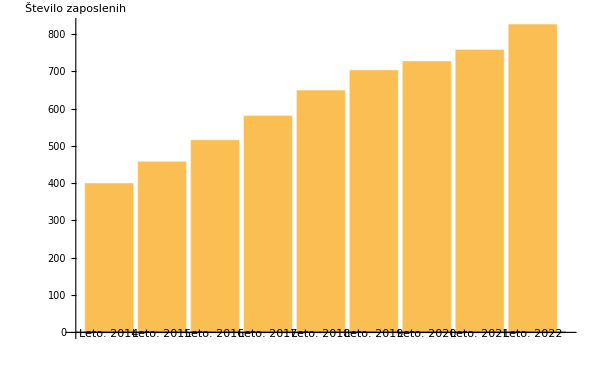
-Graphics-Diagram: Število zaposlenih skozi leta.

```mathematica
Labeled[BarChart[{399,457,515,580,648,702,726,757,825},
                                   ChartLabels->Table[leta[leto],
                                                                         {leto,2014,2022}],
                                   ImageSize->{600,400},
                                   AxesLabel->{None,"Število zaposlenih"}],
	       Text["Diagram: Število zaposlenih skozi leta."]]
```

```mathematica
zaposleneŽenske={{490},{509},{504},{542},{586}}
```

{{490},{509},{504},{542},{586}}

```mathematica
zaposleniMoški={{231},{262},{260},{278},{303}}
```

{{231},{262},{260},{278},{303}}

```mathematica
skupajZaposleni=MapThread[Plus,{zaposleneŽenske,zaposleniMoški}]
```

{{721},{771},{764},{820},{889}}

```mathematica
Labeled[Framed[TableForm[{zaposleneŽenske,
                                                   Round[100*zaposleneŽenske/skupajZaposleni],
                                                   zaposleniMoški,
                                                    Round[100*zaposleniMoški/skupajZaposleni]}, 
                                                      TableHeadings->{{"Zaposlene ženske","Odstotek žensk (%)","Zaposleni moški","Odstotek moških (%)"}, 
                                                                                        {"2018","2019","2020","2021","2022"}}]],      
                Text["Tabela: Število in odstotek zaposlenih glede na spol."]]
```

| 2018 | 2019 | 2020 | 2021 | 2022
Zaposlene ženske | 490 | 509 | 504 | 542 | 586
Odstotek žensk (%) | 68 | 66 | 66 | 66 | 66
Zaposleni moški | 231 | 262 | 260 | 278 | 303
Odstotek moških (%) | 32 | 34 | 34 | 34 | 34Tabela: Število in odstotek zaposlenih glede na spol.

```mathematica
Labeled[Import["C:\\Users\\HP\\Desktop\\Računalniška orodja v matematiki\\Vrsta zaposlitve.xlsx","Dataset","HeaderLines"->1]//First,
                Text["Tabela: Število zaposlitev za določen / nedoločen čas in število na novo sklenjenih / prekinjenih delovnih razmerij."]]
```

Tabela: Število zaposlitev za določen / nedoločen čas in število na novo sklenjenih / prekinjenih delovnih razmerij.

```mathematica
Labeled[Import["C:\\Users\\HP\\Desktop\\Računalniška orodja v matematiki\\Povprečna plača.xlsx","Dataset","HeaderLines"->1]//First//
                              Query[All,
                                         <|#,"Povprečna mesečna plača (€)"->#["Stroški plač (€)"]/12/#["Število zaposlenih"]|>&],
                Text["Tabela: Stroški plač in povprečna mesečna plača."]]
```

Tabela: Stroški plač in povprečna mesečna plača.

## RAČUNOVODSKI IZKAZ

```mathematica
podatkiZaRačunovodskiIzkaz=Import["C:\\Users\\HP\\Desktop\\Računalniška orodja v matematiki\\Računovoski izkaz.xlsx","Dataset","HeaderLines"->1]//First
```

```mathematica
podatkiZaRačunovodskiIzkaz//Query[All,<|#,"Skupaj (€)"->#["Dolgoročna sredstva (€)"]+#["Kratkoročna sredstva (€)"]+#["Kratkoročne časovne razmejitve (€)"]|>&]
```